# Exercise 1.2

## Band structure of the disordered SSH model with nearest-neighbours interactions and OBC.

The following cell evaluates a random symmetric tridiagonal matrix representing the Hamiltonian of a disordered SSH model with only nearest neighbours coupling. The disorder is a random number between -R and R, so we simply compute a random number between -1 and 1 and plot E/R. The system has open boundary conditions (OBC).

```mathematica
ClearAll[n,r,mu,psi1,psi2];
n=50;
r=2.5; (*r=R/w*)
mu=0.4; (*mu=v/w*)
Niter=100; (*number of iterations for averaging randomness*)

p={}; (*list of edge probabilities. Each element comes from different realization of randomness*)
e={};(*list of energies*)

For[i=1,i≤Niter,i++,

mat=Table[
If[OddQ[i],
(mu+r*RandomReal[{-1,1}])*KroneckerDelta[j,i+1],
##&[]]
If[EvenQ[i],
(1.0+r*RandomReal[{-1,1}])*KroneckerDelta[j,i+1],
##&[]]
,{i,1,2n},{j,1,2n}];
H=ArrayFlatten[mat + Transpose[mat]];

(*
ListPlot[Table[{0,energy[[i]]},{i,1,2n}],
PlotStyle->{Red,PointSize[.03]},Ticks->{None,Automatic},AxesStyle->Directive[Black, 12],AxesLabel->{None,"E/R"}]*)
energy=Eigenvalues[H];
{psi1,psi2}=Eigenvectors[H,-2];
(*ListPlot[{psi1^2,psi2^2},PlotRange->All,PlotStyle->{{Blue,PointSize[.02]},{Red,PointSize[.015]}},AxesLabel->{"x/a","|ψ|^2"},AxesStyle->Directive[Black, 12]]*)

(*
Pleft=psi2[[1]]^2+psi2[[2]]^2 +psi2[[2n-1]]^2+psi2[[2n]]^2;probability of finding the electron in the left edge
Pright=psi1[[1]]^2+psi1[[2]]^2+psi1[[2n-1]]^2+psi1[[2n]]^2;probability of finding the electron in the right edge*)

Pedge=psi1[[1]]^2+psi1[[2]]^2+psi1[[2n-1]]^2+psi1[[2n]]^2;
AppendTo[p,Pedge];
AppendTo[e,energy];
]
Dimensions[p]
Dimensions[e]
Mean[p]
```

{100}

{100,100}

0.143541

{10000,2}

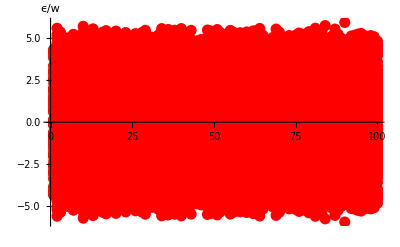

```mathematica
list={};
For[i=1,i≤Niter,i++,
For[j=1,j≤2n,j++,
AppendTo[list,{i,e[[i,j]]}]
];
]
Dimensions[list]

ListPlot[list,PlotStyle->{Red,PointSize[.02]},AxesLabel->{None,"ϵ/w"}
]
```

Now we compute the probability of being at the edges as a function of the randomness strength R (again with OBC).

```mathematica
ClearAll[r,mu,n,list];
mu=0.0;
n=50;
list={};
Niter=100;
dr=0.25;
r=0.0;

While[r≤4.0,

p={};

For[i=1,i≤Niter,i++,
mat=Table[
If[OddQ[i],
(mu+r*RandomReal[{-1,1}])*KroneckerDelta[j,i+1],
##&[]]
If[EvenQ[i],
(1.0+r*RandomReal[{-1,1}])*KroneckerDelta[j,i+1],
##&[]]
,{i,1,2n},{j,1,2n}];
H=ArrayFlatten[mat + Transpose[mat]];

{psi1,psi2}=Eigenvectors[H,-2];
Pedge=psi1[[1]]^2+psi1[[2]]^2 +psi1[[2n-1]]^2+psi1[[2n]]^2;

AppendTo[p,Pedge];
];

AppendTo[list,{r,Mean[p]}];
Clear[p];
r+=dr;
]
```

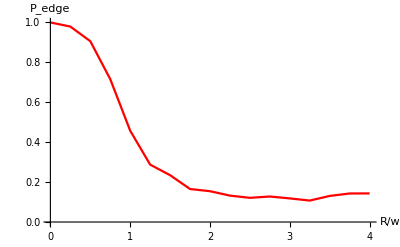

```mathematica
ListPlot[list,PlotStyle->{Red,PointSize[.015]},AxesLabel->{"R/w","P_edge"},AxesStyle->Directive[Black, 12],PlotRange->All,Joined->True]
Export["C:\\Users\\matte\\Desktop\\Ph.D\\Solid state problems\\Berry phases\\mu0.txt",list];
```

## Band structure of the disordered SSH model with nearest-neighbours interactions and PBC.

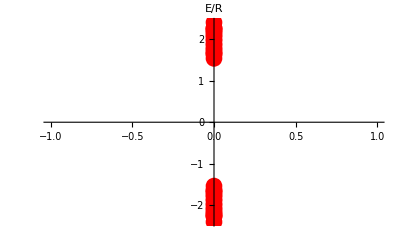

```mathematica
ClearAll;
mu=0.5;
r=2;
n=20;
mat=SparseArray[{
{i_,j_}/;j==i+1&&Mod[j,2]==1->1.+r*RandomReal[{-1,1}],
{i_,j_}/;j==i+1&&Mod[j,2]==0->mu+r*RandomReal[{-1,1}],
{1,2n}->1.+r*RandomReal[{-1,1}]
},
{2n,2n},0.];
H=mat+Transpose[mat];
energy=Eigenvalues[H];
ListPlot[Table[{0,energy[[i]]},{i,1,2n}],
PlotStyle->{Red,PointSize[.03]},Ticks->{None,Automatic},AxesStyle->Directive[Black, 12],AxesLabel->{None,"E/R"}]
```

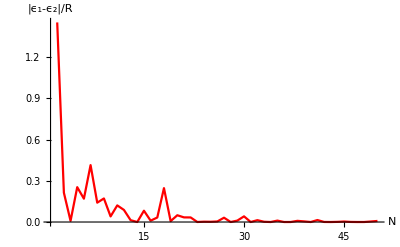

```mathematica
ClearAll;
list={};
For[k=2,k≤ 50,k+=1,
mat=SparseArray[
Table[
{i,i+1}->RandomReal[{-1,1}],
{i,1,2k-1}
],
{2k,2k},0.];
H=mat+Transpose[mat];
{e1,e2}=Eigenvalues[H,-2];
AppendTo[list,{k,2*Abs[e1-e2]}];
]
ListPlot[list,PlotStyle->{Red,PointSize[.015]},AxesLabel->{"N","|ϵ_1-ϵ_2|/R"},AxesStyle->Directive[Black, 12],PlotRange->All,Joined->True]
```

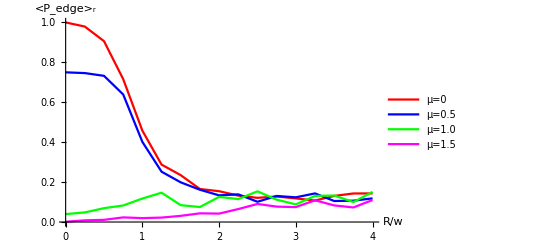

```mathematica
data0=Import["C:\\Users\\matte\\Desktop\\Ph.D\\Solid state problems\\Berry phases\\mu0.txt","Table"];
data05=Import["C:\\Users\\matte\\Desktop\\Ph.D\\Solid state problems\\Berry phases\\mu05.txt","Table"];
data1=Import["C:\\Users\\matte\\Desktop\\Ph.D\\Solid state problems\\Berry phases\\mu1.txt","Table"];
data15=Import["C:\\Users\\matte\\Desktop\\Ph.D\\Solid state problems\\Berry phases\\mu15.txt","Table"];
ListPlot[{data0,data05,data1,data15},Joined->True,AxesStyle->Directive[Black, 12],AxesLabel->{"R/w","<P_edge>_r"},PlotStyle->{Red,Blue,Green,Magenta},PlotRange->All,PlotLegends->Placed[{"μ=0","μ=0.5","μ=1.0","μ=1.5"},{0.8,0.8}]]
```